```mathematica
(*Constants*)
μ0=(4π 10^-7)(10^4);(*[Gauss m/A]*)
```

```mathematica
(*Horizontal (X,Y) trim coil calculations*)
```

```mathematica
(*Magnetic fields for wires symmetric about along xy, xz, or yz planes*)
Bxwire[x_,y_,z_,i_,n_,L_]:=(μ0 n i)/(4π){0,-2((L/2) z)/((y^2+z^2)√((L/2)^2+(y^2+z^2))),2((L/2) y)/((y^2+z^2)√((L/2)^2+(y^2+z^2)))};
Bywire[x_,y_,z_,i_,n_,L_]:=(μ0 n i)/(4π){2((L/2) z)/((x^2+z^2) √((L/2)^2+(x^2+z^2))),0,-2((L/2) x)/((x^2+z^2) √((L/2)^2+(x^2+z^2)))};
Bzwire[x_,y_,z_,i_,n_,L_]:=(μ0 n i)/(4π){-2((L/2) y)/((x^2+y^2) √((L/2)^2+(x^2+y^2))),2((L/2) x)/((x^2+y^2) √((L/2)^2+(x^2+y^2))) ,0};
```

```mathematica
(*X-axis rectangular Helmholtz coils centered at (0,0,0)*)
Bxrect[x_,y_,z_,i_,n_,l_,h_]:=Bywire[x,0,z+h/2,i,n,l]+Bywire[x,0,z-h/2,-i,n,l]+Bzwire[x,y-l/2,0,i,n,l]+Bzwire[x,y+l/2,0,-i,n,l];
```

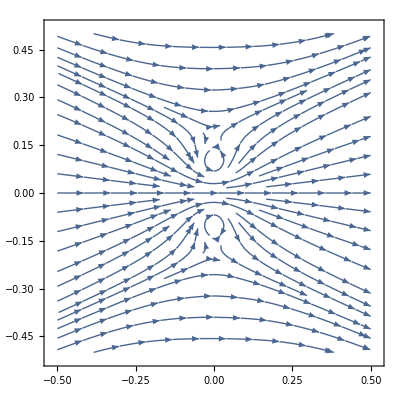

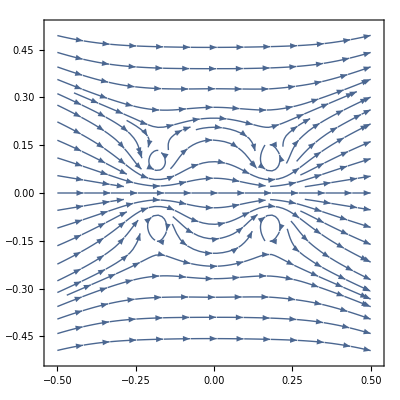

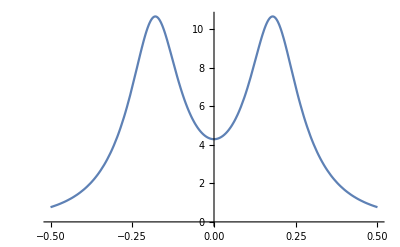

4.29093

```mathematica
(*X-axis rectangular Helmholtz coils*)
d=14.25(25.4/1000);(*[m] Separation*)
l=13.5(25.4/1000);(*[m] coil length*)
h=7(25.4/1000);(*[m] coiil height*)
StreamPlot[{Bxrect[x,0,z,1,1,l,h][[1]],Bxrect[x,0,z,1,1,l,h][[3]]},{x,-.5,.5},{z,-.5,.5}]
StreamPlot[{(Bxrect[x+d/2,0,z,1,1,l,h]+Bxrect[x-d/2,0,z,1,1,l,h])[[1]],(Bxrect[x+d/2,0,z,1,1,l,h]+Bxrect[x-d/2,0,z,1,1,l,h])[[3]]},{x,-.5,.5},{z,-.5,.5}]
Plot[{(Bxrect[x+d/2,0,0,4,45,l,h]+Bxrect[x-d/2,0,0,4,45,l,h])[[1]]},{x,-.5,.5}]
(Bxrect[0+d/2,0,0,4,45,l,h]+Bxrect[0-d/2,0,0,4,45,l,h])[[1]]
```

```mathematica
h
```

```mathematica
18.25-4.5
```

13.75